# Математические модели динамики численности одного вида

## Задание 1. Модель Мальтуса.

Простейшая модель численности популяции одного вида . Характеристики :
1. Популяция больших размеров (численность измеряется миллионами).
2. Не существует факторов сдерживания роста популяции:
	1) Болезни;
	2) Хищники;
	3) Конкурирующие виды;
	4) Ограниченность питания и др.
3. Пренебрегаем процессами иммиграции и эммиграции.
4. Случайные различия между различными особями игнорируются.
5. Каждая особь имеет равные шансы родиться и умереть с течением времени.

Концепция:
1. Численность популяции - это непрерывная функция от времени N(t).
2. Рождаемость и смертность непрерывны во времени и заданы коэффициентами на одну особь в единицу времени.
3. N’(t) = (a - b) * N(t).
4. N(t0) = N0.

#### 1.1

```mathematica
ClearAll[t0,N0];
sol=DSolveValue[{NN'[t]==(α-β)NN[t],NN[t0]==N0},NN[t],t]
```

ⅇ^(t α-t0 α-t β+t0 β) N0

```mathematica
getMaltusSolution[α_,β_,N0_,t0_]:=N0*Exp[(α-β)(t-t0)]
```

#### 1.2

```mathematica
t0=0;
N0=10;
sol=getMaltusSolution[α,β,N0,t0]
```

10 ⅇ^(t (α-β))

```mathematica
funcs=(sol/.#)&/@{{α->0,β->2},{α->2,β->2},{α->2,β->0}}
```

{10 ⅇ^(-2 t),10,10 ⅇ^(2 t),10 ⅇ^(-0.1 t)}

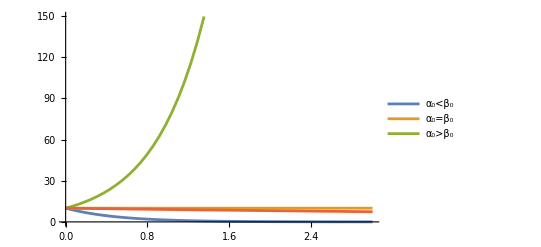

```mathematica
Plot[funcs,{t,t0,3},PlotLegends->{"α_0<β_0","α_0=β_0","α_0>β_0"}]
```

При t -> ∞ для ...
	 1) случаю, когда коэффициенты рождаемости и смертности совпадают, решением будет константа N0, значит N’(t) = 0, нет ни роста, ни падения численности. Поведение такого решения неизменно.
	2) для случая, когда коэффициент рождаемости больше, чем коэффициент смертности, решением будет экспоненциальная функция e^t. Будет наблюдаться экспоненциальный рост численности населения.
	3) для случая, когда коэффициент рождаемости меньше, чем коэффициент смертности, решением будет e^-t, что означает экспоненциальное убывание численности населения. Если брать во внимание предельное значение решения, можно сказать, что популяция вымрет.

Устойчивость решения относится к поведению решения в ответ на малые изменения входных данных или начальных условий. Положение равновесия, соответствующее решению модели при совпадении коэффициентов рождаемости и смертности устойчиво, если коэффициенты изменяются вместе, согласно условию их совпадения. Иначе неустойчиво.

#### 1.4

1) Коэффициент рождаемости меньше коэффициента смертности.

```mathematica
α=1;
β=2;
```

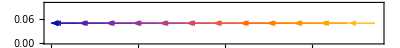

```mathematica
StreamPlot[{(α-β)x,0},{x,0,3},{y,0,0.1},AspectRatio->Automatic,ImageSize->{{300,500}}]
```

2) Коэффициент рождаемости совпадает с коэффициентом смертности.

```mathematica
α=1;
β=1;
```

```mathematica
StreamPlot[{(α-β)x,0},{x,0,3},{y,0,0.1},AspectRatio->Automatic,ImageSize->{{300,500}}]
```

-Graphics-

3) Коэффициент рождаемости больше коэффициента смертности.

```mathematica
α=2;
β=1;
```

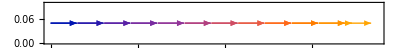

```mathematica
StreamPlot[{(α-β)x,0},{x,0,3},{y,0,0.1},AspectRatio->Automatic,ImageSize->{{300,500}}]
```

В случаях 1), 3) все близкие траектории в фазовом пространстве стремятся к положению равновесия или траектории со временем. Cистема стабилизируется вокруг этого положения равновесия.

## Задание 2. Модель Ферхюльста.

Сдерживающим фактором является ограниченность ресурсов.
	Np - это равновесная численность популяции, которую может обеспечить окружающая среда.

#### 2.1

```mathematica
-Graphics-
-Graphics-
```

```mathematica
ClearAll[t0,N0];
sol=DSolveValue[{NN'[t]==NN[t]*k(1-NN[t]/Np),NN[t0]==N0},NN[t],t]
```

(10 ⅇ^(4 t) N0)/(10 ⅇ^(4 t0)+ⅇ^(4 t) N0-ⅇ^(4 t0) N0)

```mathematica
getFerhulstSolution[k_,Np_,N0_,t0_]:=(Np*N0)/(N0+(Np-N0)*Exp[k(t0-t)])
```

#### 2.2

```mathematica
t0=0;
k=2;
Np=10;
sol=getFerhulstSolution[k,Np,N0,t0]
```

(10 N0)/(ⅇ^(-2 t) (10-N0)+N0)

```mathematica
funcs=(sol/.#)&/@{{N0->1},{N0->10},{N0->20}}
```

{10/(1+9 ⅇ^(-2 t)),10,200/(20-10 ⅇ^(-2 t))}

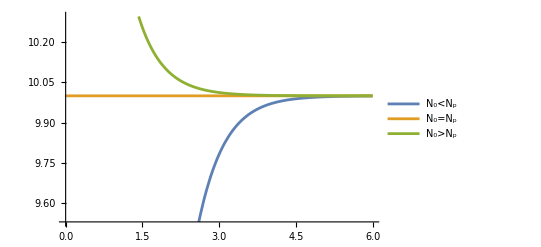

```mathematica
Plot[funcs,{t,t0,6},PlotLegends->{"N_0<N_p","N_0=N_p","N_0>N_p"}]
```

#### 2.3

При t -> ∞ наблюдается, что...
	1) для случая, когда N0 > Np выполняется свойство эффекта насыщения численности населения, то есть N(t) -> Np. Наблюдаем
	2) то же свойство выполняется и для случая, когда начальная численность популяции N0 меньше, чем равновесная численность популяции Np. То есть коэффициент отклонения численности от равновесного значения как бы настраивает численность населения, корректируя ее с течением времени. Что в принципе и согласуется с нашим пониманием окружающего мира.
	3) В случае же, когда N0 = Np сразу можно сказать, что численность населения “настроена”. Причем такое положение равновесия является устойчивым, то есть даже при небольших различиях во входных данных, получим, что N(t) -> Np.
	Чем больше коэффициент k, тем быстрее численность населения стремится к Np.

#### 2.4

1) Коэффициент рождаемости меньше коэффициента смертности.

```mathematica
t0=0;
k=10;
Np=2;
N0=5;
```

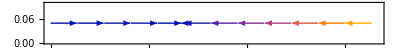

```mathematica
StreamPlot[{x*k(1-x/Np),t0},{x,0,N0},{y,0,0.1},AspectRatio->Automatic,ImageSize->{{300,500}}]
```

Положение равновесия является устойчивым.

#### 2.5

## Задание 1. Нелинейный аналог модели Мальтуса.

Особи популяции заинтересованы в росте популяции: коэффициент рождаемости пропорционален численности населения.

#### 3.1

```mathematica
-Graphics-
-Graphics-
```

```mathematica
ClearAll[t0,N0];
sol=DSolveValue[{NN'[t]==(α*NN[t]-β)NN[t],NN[t0]==N0},NN[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(ⅇ^(t0 β) N0 β)/(-ⅇ^(t β) N0 α+ⅇ^(t0 β) N0 α+ⅇ^(t β) β)

```mathematica
getNonLinearMaltusSolution[α_,β_,N0_,t0_]:=1/(α/β+(1/N0-α/β)*Exp[β(t-t0)])
```

#### 3.2

```mathematica
α=1;
β=2;
t0=0;
sol=getNonLinearMaltusSolution[α,β,N0,t0]
```

1/(1/2+ⅇ^(2 t) (-1/2+1/N0))

```mathematica
funcs=(sol/.#)&/@{{N0->1,Np->10},{N0->10,Np->10},{N0->20,Np->10},{N0->1,Np=α/β}}
```

{1/(1/2+ⅇ^(10 t)/2),1/(1/2-(2 ⅇ^(10 t))/5),1/(1/2-(9 ⅇ^(10 t))/20),1/(1/2+ⅇ^(2 t) (-1/2+1/N0))/.{N0→1,1/2}}

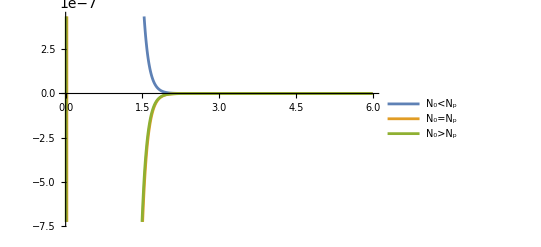

```mathematica
Plot[funcs,{t,t0,6},PlotLegends->{"N_0<N_p","N_0=N_p","N_0>N_p"}]
```

#### 3.3

#### 3.4

```mathematica
α=1;
β=2;
t0=0;
N0=5;
```

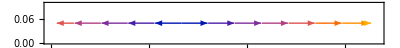

```mathematica
StreamPlot[{(α*x-β),t0},{x,0,N0},{y,0,0.1},AspectRatio->Automatic,ImageSize->{{300,500}}]
```